Jeremy’s Cool Shortcuts!

Using the @ symbol is the same as applying a function.

```mathematica
f@x
f[x]
```

f[x]

f[x]

// applies a function in reverse.

```mathematica
x//f
```

f[x]

Applying a function to lists can be done using /@ (this is a shortcut for the Map[] function).

```mathematica
f/@{x,y,z}
```

{f[x],f[y],f[z]}

A function can be made pure by using the & symbol. The pound sign (#) is used for slots.

```mathematica
f[#]&[x]
```

f[x]

NestList[] creates a list of iterative outputs. Nest[] shows just the final one. NestGraph[] fulfils an analogous purpose for graphs.

{x,f[x],f[f[x]],f[f[f[x]]]}

f[f[f[x]]]

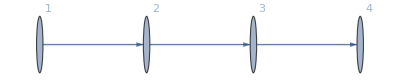

```mathematica
NestList[f,x,3]
Nest[f,x,3]
NestGraph[{#+1}&,1,3,VertexLabels->All]
```

Array acts like table but can produce n-dimensional outputs. FoldList folds elements iteratively from a list.

```mathematica
Array[f,{2,2}]//Grid
FoldList[Plus,0,Range[3]]
```

f[1,1] | f[1,2]
f[2,1] | f[2,2]

{0,1,3,6}

Items from lists can be pulled by specifying the index or span.

```mathematica
Range[10][[{1,3,5}]]
Range[10][[1;;5]]
```

{1,3,5}

{1,2,3,4,5}

The command /@ does not necessarily perform the same thing when the item a function is applied to is also a function.

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

A list can be used as the argument for a function using @@.

```mathematica
f@@{1,2,3}
```

f[1,2,3]

Three @s (@@@) applies a function to each sublist in a list.

```mathematica
f@@@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

Modules can be used while naming functions to create local variables that will not recognised outside of the function.

```mathematica
Module[{x=1},x+1]
x
```

2

x